```mathematica
(** 2D and 3D plots of the Lorentz gas Classical and Efficient algorithms **)
```

```mathematica
(* Some of the main functions have been generalized for any data input moved here for ease of access *)
```

```mathematica
sphere[r_,n_,m_,l_]:=Plot3D[{√(r^2-((x-n)^2+(y-m)^2))+l,-√(r^2-((x-n)^2+(y-m)^2))+l},{x,n-1,n+1},{y,m-1,m+1},BoxRatios->Automatic,AxesLabel->{"x", "y"},Mesh->None, PlotStyle->Directive[Opacity[0.5]]]
```

```mathematica
spheres[r_,xmin_,xmax_,ymin_,ymax_,zmin_,zmax_]:=Show[Table[sphere[r,n,m,l],{n,xmin,xmax},{m,ymin,ymax},{l,zmin,zmax}],PlotRange->All]
```

```mathematica
line[x0_,v0_,tmin_,tmax_]:=ParametricPlot3D[{x=x0[[1]]+v0[[1]]t,y=x0[[2]]+v0[[2]]t,z=x0[[3]]+v0[[3]]t},{t,tmin,tmax},PlotStyle->Directive[Thickness[0.004]]]
```

```mathematica
lorentz3d[x0_,v0_,r_,xmin_,xmax_,ymin_,ymax_,zmin_,zmax_,tmin_,tmax_]:=Show[spheres[r,xmin,xmax,ymin,ymax,zmin,zmax],line[x0,v0,tmin,tmax],ListPointPlot3D[{x0},PlotStyle->Directive[Red,PointSize[0.01]]]]
```

```mathematica
lorentz3dnostart[x0_,v0_,r_,xmin_,xmax_,ymin_,ymax_,zmin_,zmax_,tmin_,tmax_]:=Show[spheres[r,xmin,xmax,ymin,ymax,zmin,zmax],line[x0,v0,tmin,tmax]]
```

```mathematica
dist3d[x_,v_,point_]:=Norm[Cross[point-x,v]]/Norm[v]
```

```mathematica
(**********************************************************************************)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-3,3},{m,-3,3}]]],{x,-3,3},{y,-3,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
ρ:=0.3
```

```mathematica
(* Points obtained by classical algorithm *)
```

```mathematica
points:={{0.4,0.1},{0.22924952910108745,0.19350621025416642},{0.05283194463606211,0.7046886632281584},{0.06177169928112605,0.2935715537444358},{0.768731955664866,1.8089107756324223},{-1.7549257396828621,1.1730277634658894},{-1.278253524817416,1.887861799877635},{-1.700617935559081,1.9807547540651356},{-1.299563417407707,2.0161789663148117},{-1.7168158123204487,2.0990288637129226},{-1.1661377215190767,2.7502035679028825}}
```

```mathematica
(* println(collisions([0.5,0.1],[-0.42,0.23],0.3,10)[1]) *)
```

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
{{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

```mathematica
ρ:=0.1
```

```mathematica
points:={{0.0,0.35},{0.9641445552106563,0.9066491184885844},{1.901566855409655,-1.982367188367812},{1.0999748803884173,-2.9977587299757396},{1.9177056142378983,-3.9431877295644826},{-5.930360381365476,-1.07176575448247},{-4.990843003801113,-3.900420135465981},{-3.997705464350009,-2.099973672064954}}
```

```mathematica
(* Trajectory starting from (0, 0.35) *)
```

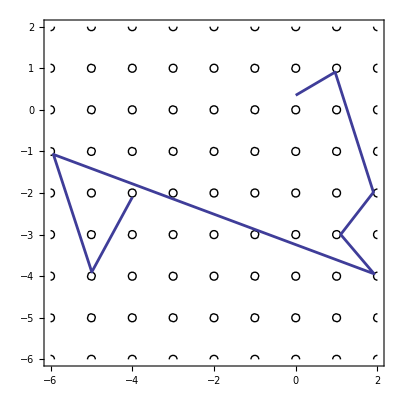

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
points:={{0,0.445},{0.94488,1.91656}}
```

```mathematica
(* Initial conditions x = (0, 0.445), v = (cos 1, sin 1), ρ = 0.1 *)
```

```mathematica
points:={{0.0,0.445},{0.94488,1.91656},{-0.971676,-0.904095},{-0.989769,-0.0994753},{-0.0924276,-4.96183},{-2.93286,-6.92589},{0.901081,-0.0146626}}
```

```mathematica
(* Classical trajectory for these initial conditions *)
```

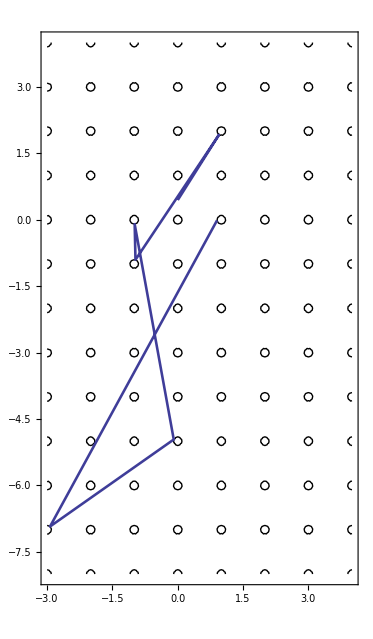

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(* The same but with a smaller radius of obstacles ρ = 0.05 *)
```

```mathematica
points2:={{0.0,0.445},{0.971899,1.95864},{-3.99055,-4.9509},{-4.96076,-1.03099},{-4.03126,-1.03902}}
```

```mathematica
ρ:=0.05
```

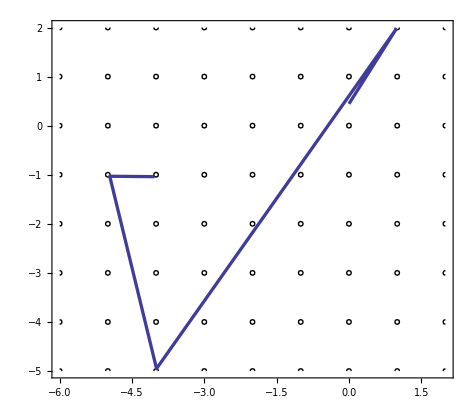

```mathematica
Show[circles,ListPlot[points2,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(* x=0; y=0.445; vx=cos(1); vy=sin(1); r=0.1 - same classical but enlarged plot *)
```

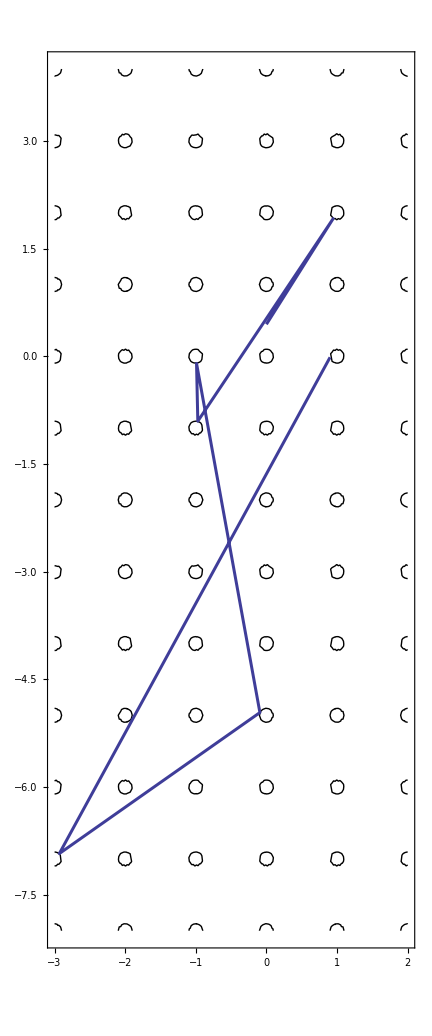

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]]]
```

```mathematica
(*********************************************************************************)
```

```mathematica
(* Trying to find the error in first_collision() of EfficientLorentz *)
```

```mathematica
x0 := {0,0.8523674178538906}
```

```mathematica
v0 := {-0.5687431776454224,-0.8225151657457678}
```

```mathematica
k := v0[[2]]/v0[[1]]
```

```mathematica
b:=x0[[2]]-k x0[[1]]
```

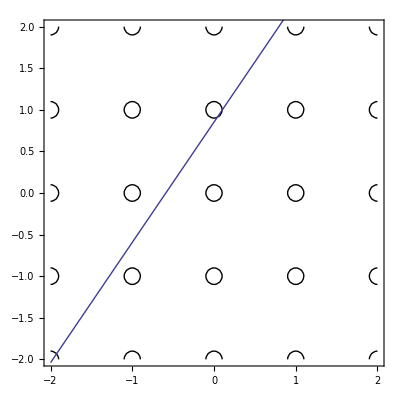

```mathematica
Show[circles,Plot[k x+b,{x,-2,2}]]
```

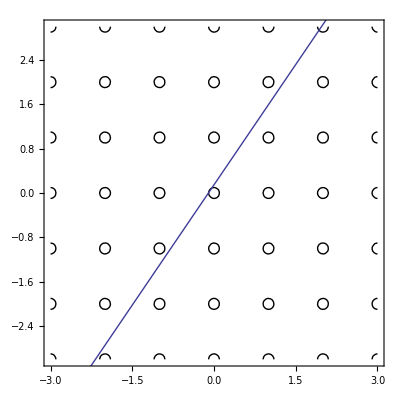

```mathematica
Show[circles,Plot[k x+1-b,{x,-3,3}]]
```

```mathematica
x0:={0,0.12}
```

```mathematica
v0={0.8,12}/Norm[{0.8,12}]
```

{0.066519,0.997785}

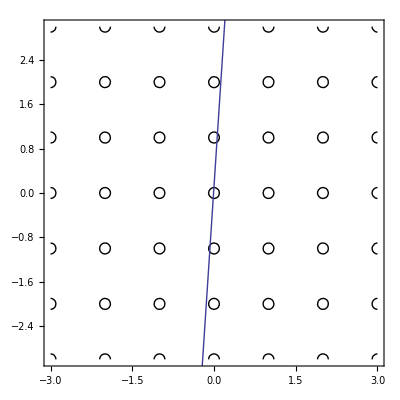

```mathematica
Show[circles,Plot[k x+b,{x,-2,2}]]
```

```mathematica
y1[x1_]:=1.2 x1+0.13
```

```mathematica
(* This formula was wrong! I found an error and fixed it. *)
```

```mathematica
dist[x_,y_,k_,b_]:=(y - k x - b)/(√(k^2+b^2))
```

```mathematica
dist[1,1,0.86,0.13]
```

0.0114973

```mathematica
dist[0,1,12,0.13]
```

0.0724957

```mathematica
dist[-1,1,-1.1,0.13]
```

-0.207646

```mathematica
dist[-1, 1, -0.9, 0.13]
```

-0.0329909

```mathematica
ϕ[b_]:=ArcTan[1-b]
```

```mathematica
l[b_]:=√(1+(1-b)^2)
```

```mathematica
dϕ[r_,b_]:=ArcSin[r/l[b]]
```

```mathematica
ψ[r_,b_]:=ArcSin[r/(1-b)]
```

```mathematica
TrigExpand[Tan[ϕ[b]-dϕ[r,b]]]
```

```mathematica
FullSimplify[-r/((1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))-(b √(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (r/(1+(1-b)^2)-(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))]
```

```mathematica
FullSimplify[(-1+b+√(2+(-2+b) b) r √(1-r^2/(2+(-2+b) b)))/(-1+r^2),b>0&&b<1&&r>0]
```

(-1+b+r √(2+(-2+b) b-r^2))/(-1+r^2)

```mathematica
TrigExpand[Tan[ϕ[b]+dϕ[r,b]]]
```

```mathematica
FullSimplify[r/((1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2))))-(b √(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2) (-r/(1+(1-b)^2)+(b r)/(1+(1-b)^2)+(√(1-r^2/(1+(1-b)^2)))/(√(1+(1-b)^2)))),b>0&&b<1&&r>0]
```

(r-(-1+b) √(2+(-2+b) b-r^2))/((-1+b) r+√(2+(-2+b) b-r^2))

```mathematica
TrigExpand[Tan[π/2-ψ[r,b]]]
```

```mathematica
FullSimplify[(√(1-r^2/(1-b)^2))/r-(b √(1-r^2/(1-b)^2))/r,b>0&&b<1&&r>0]
```

(√((-1+b)^2-r^2))/r

```mathematica
(******************************)
```

```mathematica
(* Another test: classical: collisions([0, 0.3], [cos(1.2), sin(1.2)], 0.1, 40) *)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-3,25},{m,0,3}]]],{x,-3,25},{y,0,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
points:={{0.0,0.3},{1.0110656406928884,2.900614127784398},{2.9219146792616817,0.062471454962998996},{-1.9157883662346256,1.946070409434463},{-1.0335723144172106,1.094196070537321},{-0.9350814498167989,1.923936987687108},{19.969454049802543,1.0952205068592602},{21.005610680123482,1.9001575227242835},{23.964414084951475,0.093453960056057}}
```

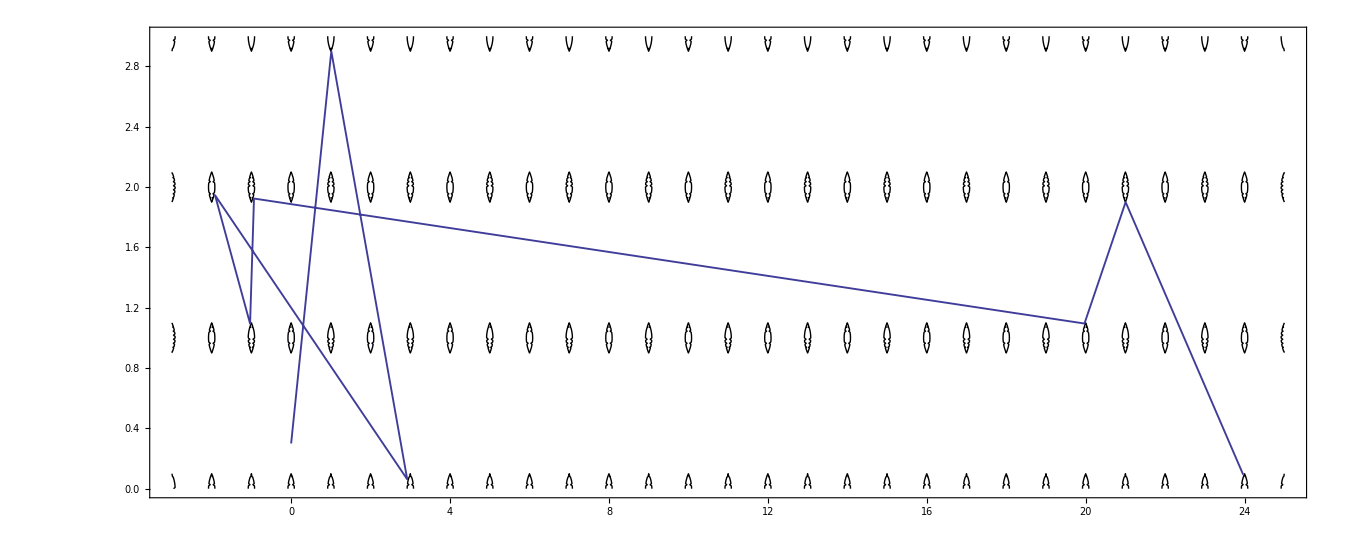

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.001]]]]
```

```mathematica
(* Finding out why and how the algorithm diverges *)
```

```mathematica
x0:={-25.9220385027411,24.062625912729082}
```

```mathematica
v0:={0.967026401228994,-0.2546761459699459}
```

```mathematica
k:=v0⟦2⟧/v0⟦1⟧
```

```mathematica
b:=x0⟦2⟧-k x0⟦1⟧
```

```mathematica
(* Stuff happens in the (-26, 25) neighborhood *)
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-27,-23},{m,23,26}]]],{x,-27,-23},{y,23,26},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
points:={{-23.91094892340575,24.045496216957076},{-24.035703610028186,24.906590941387062},{-24.999698062403922,24.099999544167403},{-25.956133158899803,24.91013510000067},{-25.9220385027411,24.062625912729082}}
```

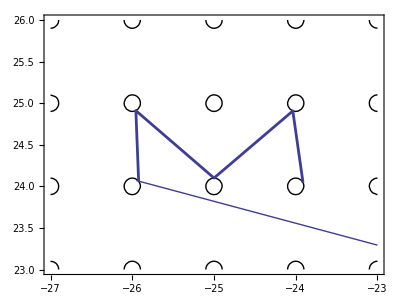

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.005]]],Plot[k x+b,{x,-25.95,-23}]]
```

```mathematica
dist[-26,24,k,b]
```

-0.00482416

```mathematica
dist[-25,24,k,b]
```

0.0104539

```mathematica
(* How is this possible?! The distance is clearly greater than 0.1! *)
```

```mathematica
line[x_]:=k x+b
```

```mathematica
line[-25]
```

23.8198

```mathematica
24-k*(-25)-b
```

0.180202

```mathematica
√(k^2+b^2)
```

17.2378

```mathematica
line[-25]-24
```

-0.180202

```mathematica
(* Error found in formula p. 69 UNAM notebook 1 *)
```

```mathematica
ρ:=0.1
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-27,2},{m,-8,27}]]],{x,-27,2},{y,-8,27},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-27,2},{-8,27}}]
```

```mathematica
points:={{0.0,0.445},{0.9448796725624946,1.9165629009182235},{-0.9716764156856601,-0.9040949710829063},{-0.9897690501214653,-0.0994752615708192},{-0.09242759468202599,-4.9618275001958825},{-2.9328562249389405,-6.925893903958246},{0.9010807499311531,-0.014662263325179836},{-23.91094892340575,24.045496216957076},{-24.035703610028186,24.906590941387062},{-24.999698062403922,24.099999544167403},{-25.956133158899803,24.91013510000067},{-25.9220385027411,24.062625912729082},{-22.085304699895232,23.05218340900884},{-22.90529612309773,23.967888075428597},{-17.071782715191617,25.069622135845716},{-16.937658041096565,25.921811252983037},{-4.091286280011369,25.04082664671126},{-4.975737295694259,25.90298803589365},{-5.900026892297164,22.99768100533914},{-5.099634509442279,20.008541927662797},{-5.981885711413208,18.09834567885268}}
```

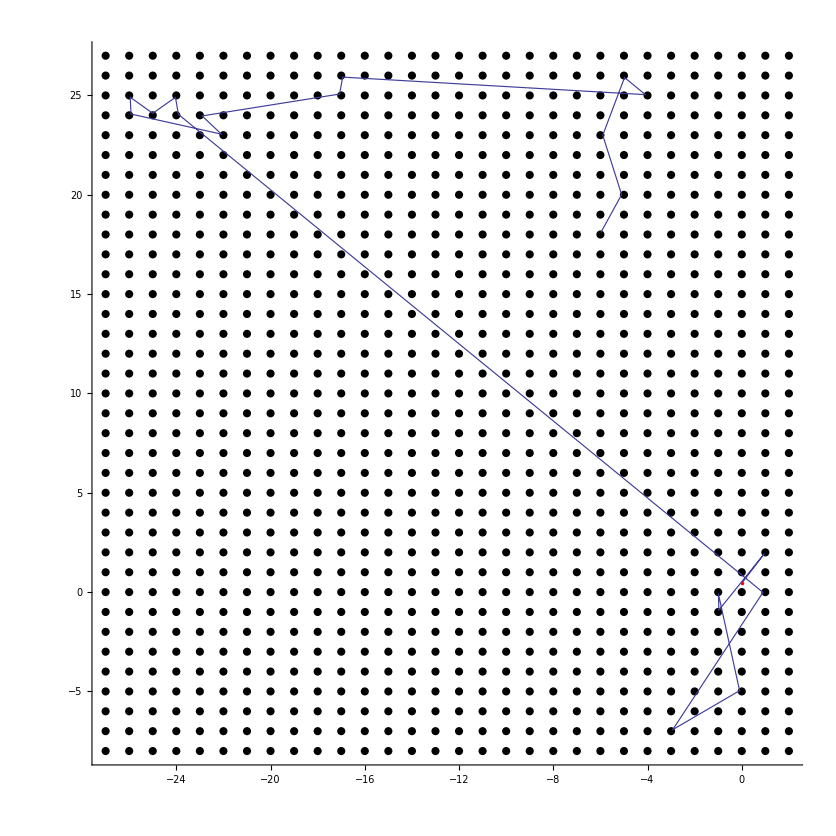

```mathematica
Show[ListPlot[Table[{n,m},{n,-27,2},{m,-8,27}],PlotStyle->Directive[PointSize->0.007,Black],AspectRatio->1],ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.001]]],ListPlot[{{0,0.445}},PlotStyle->Directive[PointSize->0.003,Red]]]
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-2,2},{m,-2,2}]]],{x,-2,2},{y,-2,2},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
x0:={0, 0.445}
```

```mathematica
v0:={0.215, 0.336}
```

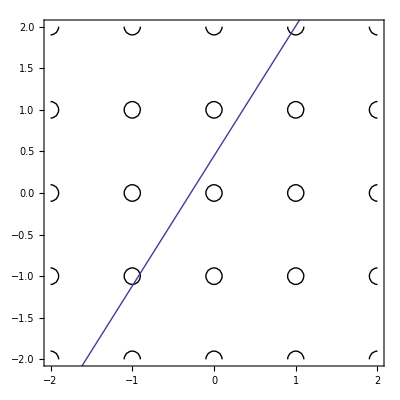

```mathematica
Show[circles,Plot[v0[[2]]/v0[[1]] x+x0[[2]],{x,-2,2}]]
```

```mathematica
(* Error when the initial position has an integer coordinate (in a particular case) *)
```

```mathematica
x0:={-2.12565,-3}
```

```mathematica
v0:={-0.536682,-0.843784}
```

```mathematica
ρ:=0.1
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-6,-1},{m,-6,-1}]]],{x,-6,-1},{y,-6,-1},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-6,-1},{-6,-1}}]
```

```mathematica
line[x]
```

0.341997+1.57222 x

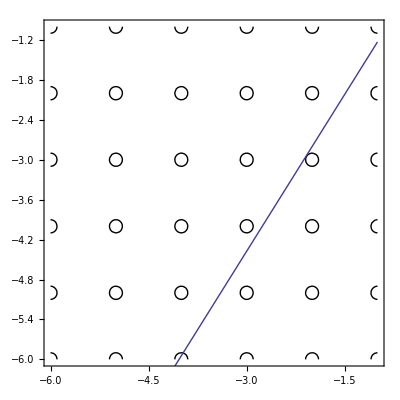

```mathematica
Show[circles,Plot[line[x],{x,-6,-1}]]
```

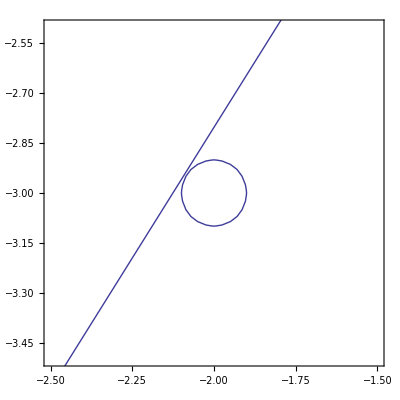

```mathematica
Show[ContourPlot[(x+2)^2+(y+3)^2==ρ^2,{x,-2.5,-1.5},{y,-3.5,-2.5}],Plot[line[x],{x,-2.5,-1.5}]]
```

```mathematica
(*********************************************************)
```

```mathematica
(* 3D version *)
```

```mathematica
x0 := {0.5,0.5,0.5}
```

```mathematica
v0:={0.1112,0.19779,0.0669}
```

```mathematica
Show[spheres[0.1,0,5,0,5,0,5],line[x0,v0,20]]
```

-Graphics3D-

```mathematica
x0:={0,0.445,0.342}
```

```mathematica
v0:={0.451207,0.541449,0.709398}
```

```mathematica
Show[spheres[0.1,2,4,3,5,4,6],line[x0,v0,4,7]]
```

-Graphics3D-

```mathematica
(* This line intersects the ball (3,4,5), but not through the center *)
```

```mathematica
v1:={-0.4512069325775071,-0.5414489190929208,-0.7093978939968069}
```

```mathematica
x1:={2.92769084745365,3.9582329100898943,4.944982736974214}
```

```mathematica
Show[spheres[0.1,-6,-1,-6,-1,-6,-1],line[x1,v1,8,16]]
```

-Graphics3D-

```mathematica
Show[spheres[0.1,-38,-36,-45,-43,-59,-57],line[x1,v1,87,90]]
```

-Graphics3D-

```mathematica
(* Distance between 3D line x⃗ = (x⃗)_0 + (v⃗)_0 t and a point p⃗ *)
```

```mathematica
distance[x0_,v0_,p_]:=Norm[x0-p-((x0-p).v0)v0]
```

```mathematica
p:={-37,-44,-58}
```

```mathematica
distance[x1,v1,p]
```

0.0994014

```mathematica
(* Less than 0.1, so this ball gets hit *)
```

```mathematica
x2:={-37.06038678750248,-44.027513426667056,-57.92519059385232}
```

```mathematica
v2:={0.4512069325775123,0.5414489190929171,0.7093978939968061}
```

```mathematica
(****)
```

```mathematica
Show[spheres[0.2,0,4,0,4,0,4],line[x0,v0,0,5]]
```

-Graphics3D-

```mathematica
x0 :={0.445,0.342}
```

```mathematica
v0:={0.60672,0.794915}
```

```mathematica
ρ:=0.2
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-1,3},{m,-1,3}]]],{x,-1,3},{y,-1,3},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-1,3},{-1,3}}]
```

```mathematica
line2d[x_,x0_,v0_]:=v0[[2]]/v0[[1]] x+x0[[2]]-v0[[2]]/v0[[1]] x0[[1]]
```

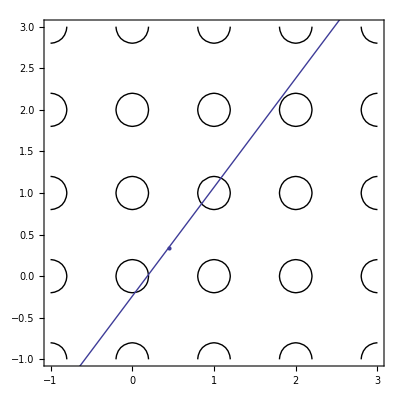

```mathematica
Show[circles,Plot[line[x,x0,v0],{x,-1,3}],ListPlot[{x0}]]
```

```mathematica
x0:={0.0,0.445};v0:={0.640184,0.768222}
```

```mathematica
v0
```

{0.640184,0.768222}

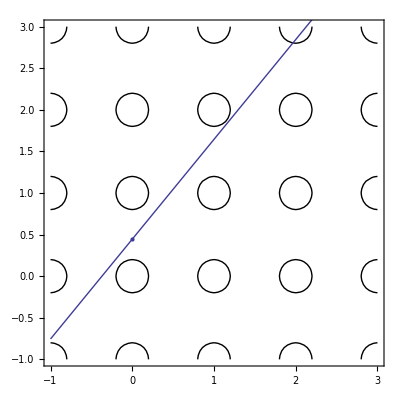

```mathematica
Show[circles,Plot[line[x,x0,v0],{x,-1,3}],ListPlot[{x0}]]
```

```mathematica
x0:={0.445,0.342};v0:={0.60672,0.794915};ρ:=0.1
```

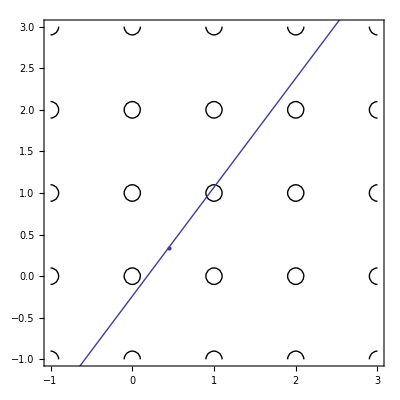

```mathematica
Show[circles,Plot[line[x,x0,v0],{x,-1,3}],ListPlot[{x0}]]
```

```mathematica
x0:={-3.96176770832104644011,9.00000000007393451476,-17.2248540924254255422}
```

```mathematica
v0:={0.492197878294012166407,0.739345146123457909362,-0.459467086423560331943}
```

```mathematica
ρ:=0.2
```

```mathematica
Show[spheres[0.2,-3,1,11,16,-21,-18],line[x0,v0,0,5]]
```

-Graphics3D-

```mathematica
p:={-2,12,-19}
```

```mathematica
distance[x0,v0,p]
```

0.0761529158922801

```mathematica
x0:={-1.81694,12.2218,-19.227}
```

```mathematica
v0:={0.492197878294012166407,0.739345146123457909362,-0.459467086423560331943}
```

```mathematica
Show[spheres[0.2,-2,0,12,15,-21,-19],line[x0,v0,0,5],ListPointPlot3D[{{-1.81694,12.2218,-19.227}}]]
```

-Graphics3D-

```mathematica
Norm[x0-{-2,12,-19}]
```

0.366381

```mathematica
x0:={-31.5646794874135777267,10.0000000000071421636,-8.86136400925839916656}
```

```mathematica
v0:={-0.995170604930726595226,0.0714216332842911117977,0.0673380826933461717346}
```

```mathematica
Show[spheres[0.2,-32,-30,10,11,-9,-8],line[x0,v0,0,1],ListPointPlot3D[{x0}]]
```

-Graphics3D-

```mathematica
distance[x0,v0,{-32,10,-9}]
```

0.1704328213849556

```mathematica
x0:={-31.5647,10.0}
```

```mathematica
v0:={-0.997435,0.0715841}
```

```mathematica
ρ:=0.2
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-33,-30},{m,9,11}]]],{x,-33,-30},{y,9,11},Axes->True,AspectRatio->Automatic,ContourStyle->Black,PlotRange->{{-33,-30},{9,11}}]
```

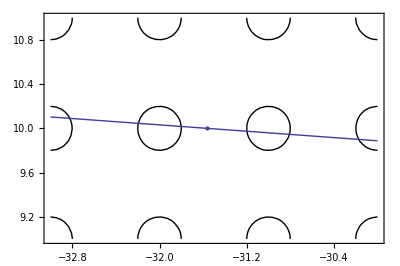

```mathematica
Show[circles,Plot[line2d[x,x0,v0],{x,-33,-30}],ListPlot[{x0}]]
```

```mathematica
(******************************************************************************)
```

```mathematica
(* Resolving the problem: C and E agree on the first collision and the immediate-afterward coord and speed, but the E misses obstacles which C finds. Need to see simulation *)
```

```mathematica
x0:={2.88124933590079817603,3.90250303447010145775,4.87196632673995360611}
```

```mathematica
v0:={-0.719660173353565737683,-0.419859303753652908205,-0.552998553289439927704}
```

```mathematica
lorentz3d[0.2,-2,3,0,4,0,5,0,8]
```

-Graphics3D-

```mathematica
lorentz3dnostart[0.2,-2,1,0,2,0,2,5,8]
```

-Graphics3D-

```mathematica
(* David Sanders' idea: take x={0,0,0} and v = {2/3, 2/3, 1/3}. It hits (2,2,1). In xy-plane, it "hits" both (1,1) and (2,2), and in yz- and xz-planes it "hits" (2,1). The initial values are too "exact", so the E algorithm may stall. We "smudge" the values a bit. *)
```

```mathematica
v0:={2/3, 2/3, 1/3}
```

```mathematica
x0:=v0*0.8
```

```mathematica
lorentz3d[x0,v0,0.2,0,2,0,2,0,2,0,3]
```

-Graphics3D-

```mathematica
x0:={10.0764053422964544949,26.029067229247587742,6.81746967415678619328}
```

```mathematica
v0:={0.837062156955717057171,-0.493583634870910865824,-0.236013009769084225237}
```

```mathematica
lorentz3d[x0,v0,0.2,8,10,25,28,4,7,0,5]
```

-Graphics3D-

```mathematica
dist3d[x0,v0,{10,26,7}]
```

0.17719445859133287

```mathematica
x0:={16.8289990492993435135,22.0452392128352392103,4.90666143090062079925}
```

```mathematica
v0:={-0.388641823164963131992,-0.169475879050012219677,-0.905668515356054074767}
```

```mathematica
(* Zoom in at the arguable place *)
```

```mathematica
lorentz3dnostart[x0,v0,0.2,12,14,20,22,-6,-2,7,12]
```

-Graphics3D-

```mathematica
(* x=[0.532282,0.531928,0.267589];v=[0.665341,0.668661,0.331986];r=0.15. Hits (2,2,1). Afterwards: *)
```

```mathematica
x0:={1.89717182844582602939,1.90362852285732340833,0.948629721354036554277}
```

```mathematica
v0:={-0.704877071895435892979,-0.615519586395728865533,-0.352539291823404229151}
```

```mathematica
lorentz3dnostart[x0,v0,0.15,-7,-5,-7,-4,-4,-3,10,15]
```

-Graphics3D-

```mathematica
x0:={10.0763022243879987808,26.029033106971180736,6.81742111498575890103}
```

```mathematica
v0:={0.836793467368476666293,-0.493671312143907367321,-0.236781182815600773207}
```

```mathematica
lorentz3d[x0,v0,0.2,12,13,20,21,-6,-2,0,15]
```

-Graphics3D-

```mathematica
(*???????????????????? What? I'll see tomorrow. *)
```

```mathematica
x0:={-4.03108362719620705447,-2.90699675491303412365,-2.01960113577374986778}
```

```mathematica
v0:={-8.79327751905091057835,-1.21256670037629447435,-4.60520927538504037778}/10
```

```mathematica
lorentz3dnostart[x0,v0,0.1,-28,-26,-7,-5,-15,-13,25,28]
```

-Graphics3D-

```mathematica
dist3d[x0,v0,{-27,-6,-14}]
```

0.08319371506054963

```mathematica
(* Hits! C is right. E missed it. *)
```

```mathematica
lorentz3dnostart[x0,v0,0.1,-72,-70,-13,-9,-39,-36,73,78]
```

-Graphics3D-

```mathematica
(* E is completely wrong. *)
```

```mathematica
(* Bigger balls *)
```

```mathematica
x0:={9.03873664987589181931*10^-02,2.28535248115236243262*10^-01,4.58450035044872204466*10^-02}
```

```mathematica
v0:={-4.23587770898546668598*10^-02,9.98969443297411327845*10^-01,-1.63029249373263497814*10^-02}
```

```mathematica
lorentz3dnostart[x0,v0,0.25,0,2,0,2,0,2,0,3]
```

-Graphics3D-

```mathematica
x0:={6.7756978219103365775*10^-02,7.62239663929128527552*10^-01,3.71350844092511238316*10^-02}
```

```mathematica
v0:={4.801631428705712938*10^-01,-8.34568452865158919073*10^-01,2.70071941732032495213*10^-01}
```

```mathematica
lorentz3dnostart[x0,v0,0.25,3,4,-6,-4,2,3,5,9]
```

-Graphics3D-

```mathematica
x0:={1.89717182844582602939,1.90362852285732340833,9.48629721354036554277*10^-01}
```

```mathematica
v0:={-7.04877071895435892979,-6.15519586395728865533,-3.52539291823404229151}/10
```

```mathematica
lorentz3dnostart[x0,v0,0.15,-7,-5,-7,-5,-5,-3,9,15]
```

-Graphics3D-

```mathematica
x0:={1.889260537279145903*10^-01,2.78741431232908856708*10^-01,9.54471620166186795206*10^-2}
```

```mathematica
v0:={3.7118555964013705636,9.0861189019905797752,1.91430701047489417523}/10
```

```mathematica
lorentz3dnostart[x0,v0,0.35,1,2,4,5,1,2,3,5]
```

-Graphics3D-

```mathematica
x0:={1.12572305500350674872,-1.70728533206424794712,-1.44954601913314947928*10^-01};v0:={7.73314394646670227732*10^-01,-4.20129722929722670938*10^-01,-4.74842987674082045945*10^-01}
```

```mathematica
Show[lorentz3d[x0,v0,0.35,1,4,-3,-1,-2,0,0,5],ListPointPlot3D[{{3.64608,-3.07656,-1.69255}},PlotStyle->Directive[Yellow,PointSize[0.01]]]]
```

-Graphics3D-

```mathematica
dist3d[x0,v0,{2,-2,-1}]
```

0.359059227809254582

```mathematica
lorentz3dnostart[x0,v0,0.35,-8,-6,-4,-2,3,5,6,10]
```

-Graphics3D-

```mathematica
x0:={2.2000297927544893278*10^+01,9.06653611895305306572*10^-01,4.09964134096038358257*10^+02};v0:={5.44662959760666846806*10^-02,-6.69060196931100424123*10^-01,7.41209737851011116032*10^-01}
```

```mathematica
dist3d[x0,v0,{25,-37,452}]
```

0.092015193081842

```mathematica
lorentz3d[x0,v0,0.1,21,23,-1,1,410,412,0,3]
```

-Graphics3D-

```mathematica
dist3d[{1.68289992589530794861*10^+01,2.20452390937991342373*10^+01,4.9066609891115339926},{-3.88637381921072624002*10^-01,-1.69477505754780016331*10^-01,-9.05670116773581549492*10^-01},{12,20,-6}]
```

0.136841686882

```mathematica
dist3d[{1.6826039108160662925*10^+01,2.20490655764205842147*10^+01,4.91438354526740620596},{-4.64404055655824731831*10^-01,-1.26505786289427920764*10^-01,-8.765415900718660343*10^-01},{13,21,-2}]
```

0.14953141781651

```mathematica
(* Although E and C diverge, they seem to hit correct balls (in their own opinion). Let's swap and see if the distance will be > 0.2 *)
```

```mathematica
dist3d[{1.68289992589530794861*10^+01,2.20452390937991342373*10^+01,4.9066609891115339926},{-3.88637381921072624002*10^-01,-1.69477505754780016331*10^-01,-9.05670116773581549492*10^-01},{13,21,-2}]
```

0.850351248257277

```mathematica
dist3d[{1.6826039108160662925*10^+01,2.20490655764205842147*10^+01,4.91438354526740620596},{-4.64404055655824731831*10^-01,-1.26505786289427920764*10^-01,-8.765415900718660343*10^-01},{12,20,-6}]
```

0.9959258529530614

```mathematica
(*************)
```

```mathematica
dist3d[{1.89430371663748794661,2.88306486791354630531,1.91308354259822142819},{5.68095923372402998103*10^-02,-8.414063192665022675*10^-01,-5.37408667697938626537*10^-01},{2,0,0}]
```

0.1092245320363806

```mathematica
dist3d[{1.89430371663748794661,2.88306486791354630531,1.91308354259822142819},{5.68095923372402998103*10^-02,-8.414063192665022675*10^-01,-5.37408667697938626537*10^-01},{3,-11,-7}]
```

0.17110681754214

```mathematica
x0:={4.1490000994502035404181066706385803645368573084362382909259365694295624140282426901676275992120619498375949547500243520043001840639675892622363180381432804840654541106904770039027533279642349864152372759426042548271801642478885976262736329235926478904192821807358550358901399468018325712960460366421124586818243150517937056194139408209212096728672174797471587460992096026862805969643318105426797154742556758369266016044933192607444468251006789147677816198396220232260641235562297919307430601432945581415922716154497804290588505844885441960255184059394480233586817617855834898527304049542868444491623045115899013864945709524897586187118393132334940446701910382258302225493369866604865231473392549758030771446004387973980569671581283891742592270294268045953623168594726170279717236258326351899666194600794719580051210717800968072460006084516970234077737492390217220266767641319051673259006713635722482028631164222950872751012023713314333421072423860738159666725332928953951975166792729016174040728802062679563011445938218605021080894421351492798342769582123660906517148194364589120754094212460254027722478317890618859774256157718739092079600132529091246437831607259806656326974350420230203231605228318429818134791117920635122032211552279*10^+03,4.7909999895282754157010584677167069055857365300529090344690077174081198830675795602807265725519697065859610629792102730077393426779142032640129717361479567433183140056230620464784382062871700175750107224249458664286547504401013096241986551387531806167793052843660686957549291588244825063662518555145735169657345016553413259055897899956948990397380803990069620160243771611497250255363966696697745654642627261320441433776763957873867080308984144819940975659632634342410420400838779133520407396800894950076623802626386253595079590332082793385035421818124007177309017588092226169207257248547656912701808390480445646863012594768064908018806036597457260256152042641957867792097840549513621606207975325240148556402520840740459017149568998785960948060596198244131809999785573829921248337274046210424353563102102066076852468132077592273138550527509716866512540879551318347893796216807491875717733025905478759656871430841854812801516465781710538050753085191262787503922023888945131078168573685041373871749109354236260457296111667691193430743795243933546884465808500173885778373548932139056994503073608581875930619710645632525876838338933579827828284715235730686629012440482891109085159244353963505523443742759114094487724567665742337254540072176*10^+03,0};v0:={9.8242622168397937449270454223963985841064192074846235430473909085374586349289109583368150641798354483864409884893363445640573750318008211802130327412656609990791725671158722279596796309808830113451975006148129359008327874403600318737670213334895420892023814601230495706279593658707485941201907508415533211969846504954260361557719021290345793353811343347363832462546196471516791555635193819801060954220547995703280483871252783871543278886728729363020439526526134850092469105117507721985905922570588171362001420345794498240406722259850717196143892621178430238358103138068665811708403184454365292540617364160477713760954558878197755105295313015374371860985145876318395606866456894155622579829723705450368085143639325532887449368934404252749714350746191164297293629414938169926955562069874152375315226005932350416439667219067804607782652964266530894425808515245154890220201115802786536027316699050703784553854881800113232684241261882711267831011400766289894155737255751940668485838268383747877214449577416891251894460135428744456485309727063281103172967404884684624228586488829262166711520847469575756744006351841673853789886769203765224936728383338858398699313671526466158915410339098648709954243370231030879064243540435633182081529687214*10^-01,1.8665132988473632287011133289643273041047022935836545506573211593937710110831343904924905771736639129628350169405226493400142658956225458277108538549851044909793852121946388486117791494025002546867493851607881748530528149713457341177935470954880507558681990066872646032509829444519359509802312308424426278289817012774539023741528111188179063627568402643433030527969029443396778257199793114760456409873188982076169996726220014157337872569998124171622899323644283131710260862707866534802323904074825017755248459757354447782782783755989062984637840915441789314780830270914321877236293975922936848767425690254449789660719354317976124736821952525674138458510898405363725813229959091989620149008324291837526439650659126204784972302033978613658228455175120182909211921185452398753211221829030615304274135707823477945831749718019893615619662040964786201953193700793739337007853816328921273700641138686925781223878225119285064934168955614404175046199504976668468750764505811551017852069475512184974076402476320435731174619682336442955270061513664253455332762172665802916625882858943238948741373750427822078229194638904105965460997478693890730927735669075456003511783629621913128502152920879313996779297281746335725556691056373886157117976870067*10^-01,0}
```

```mathematica
dist3d[x0,v0,{4097,5262,0}]
```

472.4286484173701287239278493741873805172976308673826849752447404164452864610596616525315959159027762675083435583474931998956351624398795030905081353881613964841346703039307863003238410201801779965712713223605771857949423774487110615680356797928182574921680463209243305833753927818295057932840603264898643098982968956378709185833564461456682978415944572715553763118910185244533878980677849015968381525898591388835915787408248583665608329138670238637848418094179820546185753337031035041534708556628491869824261516959341141960959173193380400025731354157955536678875038540445357294250177407143962493721537249964246840460665157771780641910133170276529909771236877765791488834803468705882088565437478512129872600770491435184486024749552691197793166499937894537840004102420587561381268952019202200507289332301045303119925007953519807508673729968635928230404194896081807097710465231208696943853356006667579889969065513630760809141653948790269231265830392514255262601798096294753043019252725027163478185776706619884481791263419258308694795042472862466084271551792256128846404196167498570471999790444753184596179316121432591140368807724463644884454998734138648448868426257951889059841765248225480389867574768339314384936875561120654893456

```mathematica
dist3d[x0,v0,{9244,5759,0}]
```

0.00008567757003548051958961337394530310613488488101480394088935026718989491474233877675874005095369732233517663543381313264554508822909239064121101049811140666520624377096290931360027044026447638812859843472293600674413026851682480551550845668613672462194659233766098660288486428447155446933258973412918881157763113733306335974262829916049944354774872654808377252367807153677518448272252306250482531668842524653159564256686575879100332625999177575324358191738284382411271346990673470775740064432332179961651570616334616733494656482815786961261003096735135308027020454353227901845775821737329564774867196019427691687420211863400507759155456087238978041935432315087154152526245287118657161039941398346879546384272320933464623339528227083484887494279428732088485086219928382267764621426691498947545153407002302275225241479450400815800824335634058696458863549831038182952251651251440669929332713144412728380402961246749615914055353038009365939182136009170978191149923744639722257787821918580377501620126016184606169272720015176522752154635588918422508746985169063472357031578434419303304568085798911848534091325866169600158272710854288877640803441233579338051482688895740056940772377074959054307433774894762325158313355509278521208

```mathematica
(* Looks like the new version gives the correct result, although the place and speed are taken from the new one. *)
```

```mathematica
(* From the old version *)
```

```mathematica
x0old:={4.1490000801144369779006415288405987959259005877788123900166850130806433426069761142546485536866693476986382602565996919476990605746934172100995599159235535582707023780665235359668351075106319231969369846909803588838696754318046084679956118554266648172282528713261926926434593955215366069849471715936049068395557857192209033603550368066392853771961928801474687159011952590336156168536569417806694892503012755361760697856815055578918444369630210599638757655318117721190328274231456988990573936172812679387397492405236028353638980011646999057991698378474690591425059314968840988647971845667582961729591804740812524651661244819718730428010961854232984396806178641144524934576465631296094079941545408525788292702451030623760025041227715943358225945035301969469421032424333567741052644534033007461128628333937763317844759065274133218595908549226557258303275023979564616401197243337060895229145520382217072084258051121634907177387548478596490847607402993032983089586065420793230618914302532650160936762830898675888197188138928299390112785114569651987261755640270446799489577120049159746428290967091138431612388034273864968133208902647167591654385881010764192253585308848792509597673400877044678943945857736557984674520323491630415421386476158*10^+03,
4.7910000598471134451277151376940789289771811029574135147498382488253850153849568737343681383626072210019527487572302816923632323286215778487514158536580265107254612589034672509868591233463664773233488955125828047051991775082866124568333039958690100737101015380684307864668277244432857223176212244668816651032887959295256218946311183339492011333042921319431624040913386774382673913049802328147299172525474150652197275623136805536001518217860369179679542015234344827976241410664849248293201730155324418287204364053962669227669974385219641486722993044472112924954154280516442965363060147424669407775439828301099333568047660317958471223050189029661408065646608767376331629193887921595321093540209363817316543514271800263202186707063457279262650407522610365668530888174254491977705778187584899234433255487006981826810048551935753509123035975456129800089398280412862749441714468736872138849575264946748214883244583493720485171826758562678254796729769429550410751320383138320870957341279097244587381565051628173016082924253887858771788563308066851419369230286248478494023106407130522933718476916425672594528277035611367333451819880166458559936225962084858905626517120762049333867435878721451947148447755183273251757109529073879588468941225739*10^+03,0}; v0old:={
-1.0973664702853605206550204637938081332398647046043408767440452777615695665026580536249204235690635252725927282487222493463247921924736746519995641375259790621541819364231327763919067816382177173932336775484176225064310695394806569017942451582235103443429046428094370734386566466832438307492076515501825668777245711007347347213286560164069702343055214743419827463900148474442901111253619949061994631417328190885660421021161899521053286737233863100358541053007497606743804207852569498336433625010292962195636009037774070060459784492722962991915164216427407121419739591406411858184234426082433807338086020220596173771421460544634388070853496634393204136520901618763136188648407202834833021624144910320550944983650070810652359470708930403904803061017968551186043329685554125802522347447764883594693559149076560043398798342240142229574368162508552191220087114639683790264471930463725651801644026948355857581899356697328807388336788286538045710964155317353617206572381629935537886021778034733672357771087170511528937000009135382570741935048396722469271769491148419796423592275433728625011271758741841013461443907927163622440913637490711533196918449096483912842141355980826065402192547469452177033478172377684259046277113970342080225845785984*10^-01,
9.9396069756250148128089136379306024550749076934426537304227192712083393398603996410670896643545948253082452284947360031075731335918597397763610090546711779031119598346615805370884361786704848491541530763372424514631068970788354316586200867539889033224617534331365844196646556348434797531468874685343877337084930734630784141153458209025734881966834593382045427611137029333468020266989098868700684160591123176615351417324540871772087769603126037813716141526514886838789015169066220921584605709407480098324736490066232506052089752037565298020421729326017250409043782472916668886592801987875142441218277711301691230336624820276540622713327748948412357025301958879303441974246668106522098682630948157876791251944551149890415673501758023921717968551900278300180919207265245797846342762331591434197595054859998312546168420431032237067814190721804144329079153519006022448110401987655741050455783224883354198203547773190096323505004549814565003666497716285776759177061550106845272818613644417310778132174110137225559341485088334067968150012767573010100820506729970949913147558170752242232698161024162720559533373049683518251033329185307069142152551255282907982874137302772826883030318457127488130567738966923353724577214790501963630184641309264*10^-01,0}
```

```mathematica
dist3d[x0old,v0old,{4097,5262,0}]
```

0.000081720832823689671921137974672390370600413018619560671137715288869899681128076727166479707039326422737498166022404485201673984952244765987895608494898242837405103748392773145579832339986490742451797907260472548143863288127863679703468198017766523720237781455181966673759865680493627142596142792581709612685681401086232876330570126797378045778220863975783659375099033072340362091377011093153186399869058405214594792329029101683024015458614735563118852055891034072775030470504689429533133649562095802452469615295595777895925265078888987926737374061896972364233335097388837642712808852599269294344233840425648329657901595409638978506937072075856029576739439829025637190930622828281371192600926299496751677409111632601701893550843102690644206916411979254191873025241368256575549319113771175380170037968204859340731128120081189228976827717465186707655803772135998816144798034328882803730273934061219325276642316002554382686584957175126174315692624799792570869669378600614444487207821635242126141882275726500934071905048161681667975839617441124602206288173530706466336849544247085777121632191142477189771722683393972434484146512028781237966028015552119494706976489281549463435786868437614947852400602024357813861063942833479750103

```mathematica
(* That's true, the old version produces its own results. But does it go backward or forward in the old version? *)
```

```mathematica
Dot[{4097,5262,0}-x0old,v0old]
```

473.861743503233137903180228532188432550678086774178154592484537079847000010058097857902043979267193005589637687221972861061726040027757751136491738553702077934682848025183229780757601306839429919671407420249501928241812025414462893394768041105294668073530619391031165710843015611284468788795770216135091085413908823533224567337339704003900354101276067167344078411762636607370423284364763784558398477399085958834350838462555286187237812661541060287338741978600699873352285981768179523396901727985716012692317844047303661429993842204581982445292141576774519456299930297014152312155058104421962897453858323618778539508275643519713544914877929397215716447083207319462431384755708256561026560688050000965023591281770305596383848844256054195369886805338350885151756834705147492536978304861491305721065132860792327458525019837625091550813776526075442443098230503124735945219456067236044328694694313645053289788004315613607398934511547078552334170730887199939568294227867681772640642657699320730634531170650555511010710194353632588898374099145350054721247039679243055129484453466736570190162066080404961738654762589322874682831447519606397300507246124915616042133133306477061401587568872597554656549866319080320751269422246181133869357609526

```mathematica
Dot[{9244,5759,0}-x0,v0]
```

5186.139991060373283509013178912196263536498530181549397099347308619718701058096072044947569666261671575013205671391839351909171362594621786986340291705588037375033814108496003853092801728241598611019025780104126353068208937804384138893347694523913941845947355365048934595161873982140309619063459504059789834994069466946049280927842543488700219102974156611482055134022203206695592569745377760047910423881420736586735362795604240424968284839097021006123964317558344200636573756434636168677994522603272287025902411744121774373983776911693373056953177727000582562122001144437655107323616138055077136844179838218630154336290743367659216503918827915328571816894749346712501290819496835776644196792657090967039350271969900090827052768299555678268738993221774524449695436249080193973350633767450471316779099479165876841191219261478105277307877647813963909662547518617307419909977021768810821322521600606694930543927098671970011906848160571916256012918122230734677264083272384495883697858534856267257047448463155571003376888948626130181019825408429114575294622399917550173309572725879826474665013789812770595461736634486403793707527379909742436520876350055512443827421420230523126785508161143676537785305927487973104415905430402169630597631136

```mathematica
(* 2D tests *)
```

```mathematica
x0:={0.01, 0.445};v0:={0.190809,-0.98162}
```

```mathematica
line2d[x0_,v0_,tmin_,tmax_]:=Plot[x0[[2]]+v0[[2]]/v0[[1]](x-x0[[1]]),{x,x0[[1]]+v0[[1]]tmin,x0[[1]]+v0[[1]]tmax}]
```

```mathematica
ρ:=0.1
```

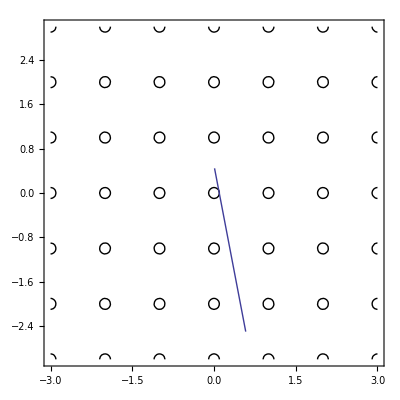

```mathematica
Show[circles,line2d[x0,v0,0,3]]
```

```mathematica
dist3d[{x0[[1]],x0[[2]],0},{v0[[1]],v0[[2]],0},{0,1,0}]
```

0.0960835

```mathematica
fline[x_]:=x0[[2]]+v0[[2]]/v0[[1]](x-x0[[1]])
```

```mathematica
fline[0]
```

0.496445

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-2,1},{m,-7,5}]]],{x,-2,1},{y,-7,5},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

```mathematica
x0:={-9.999860292006847446906356095412057579536657958431691167233288074863063892387505*10^-02,-4.999471403713147061535094488857724171182009315367484739945903776664616863563615*10^+00};v0:={-1.090324834048399604376820679437122781371239673177040749875049379590368951408611*10^-01,-9.940381871752077204641245718347970740156619164580277080802559108791169125657946*10^-01}
```

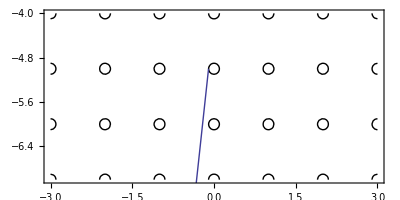

```mathematica
Show[circles,line2d[x0,v0,0,3]]
```

```mathematica
dist3d[{x0[[1]],x0[[2]],0},{v0[[1]],v0[[2]],0},{0,-4,0}]
```

0.00957241927224750785684408431497829435739199015617941004183821030836397378051

```mathematica
points:={{1.000000000000000020816681711721685132943093776702880859375*10^-02,4.45000000000000006661338147750939242541790008544921875*10^-01},{-9.812142289257714811157029544119723141193389892578125*10^-01,3.901780374643625037833771784789860248565673828125},{-9.99565080416981999178460682742297649383544921875*10^-02,-4.99705101710586330199248550343327224254608154296875}}
```

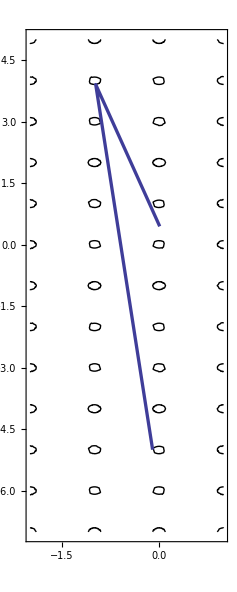

```mathematica
Show[circles,ListPlot[points,Joined->True,PlotStyle->Directive[Thickness[0.01]]]]
```

```mathematica
x0:={-93.9936955965571256473983221934688928429430897564307317292979559159233602432992017747413157187679861945299796159199790043960170900356706557506782623821079163453220277127939092138690160498496291169543206445251271365276180648831150744999,-72.099801074629632490794112514295138322392798327269044358487150156830142725231902160530577266623164451194196660004548469616144818841582671772927421647908418350886454505745710120248815457754136815691346488548434097901368445663656063865073026087281}
```

```mathematica
v0:={-0.98553266479920732740435394802910112732355424348107258246609575965321582440058005870900937047612919373828350742356971996242963025600400615364406531702714828347891552491450086730856832404646172068746506923318958885664803593560821523201116962064037114559264824939,-0.169485594118713376951991798063288288619274051434402209050738665366691670068466837509196325816470313153806898849567342711799417917522309514693000055443285054975131340841301048978002658076865537890184474842112958262337931761967168624486661210337667}
```

```mathematica
circles:=ContourPlot[Evaluate[Flatten[Table[(x-n)^2+(y-m)^2==ρ^2,{n,-100,-92},{m,-74,-71}]]],{x,-100,-92},{y,-74,-71},Axes->True,AspectRatio->Automatic,ContourStyle->Black]
```

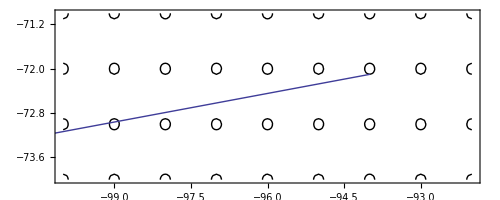

```mathematica
Show[circles,line2d[x0,v0,0,10]]
```

```mathematica
xminus1:={-75.07623513166793608911488941929506994843965926778479408191884981629605753748422152450602089131081396444849057059956027292619737220460315441612843502174889012175148705371634538363818261738809001166545664898445807842569162475999, -72.935283659717406392516946292028619810677149548501532053343837513966111597496106282295912040401510331668146053826288658965569487758716788694275930940540989848493390107929795655149814657129780201774278747802236496152555}
```

```mathematica
vminus1:={-0.99902616723598053924545056698443627407042627154968307126277731944608993709231386139214338386476112945360941033707027302050483502562255430449418429132795705671491170846478046448873426881804967039470851933254407848356718858094920884563, 0.0441216180322825845294240522712779539381772444929302740933918125544443935373304438667149204024194467106317606276214555530866118694084577575674498096674637084220652715538374601830667398143249799106349251749606920210284163867593490801710948}
```

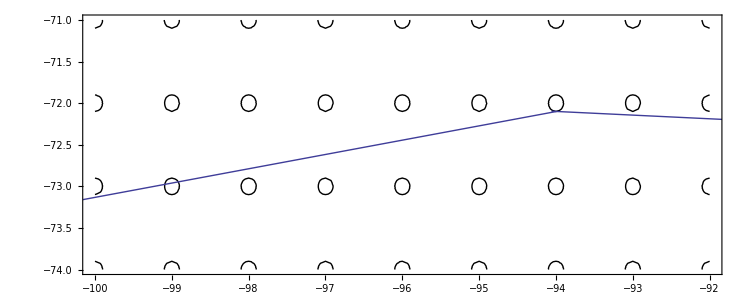

```mathematica
Show[circles,line2d[x0,v0,0,10],line2d[xminus1,vminus1,0,19]]
```

```mathematica
(* Efficient goes backwards on this very rare step, to (-93, -72)! Fixed. *)
```

```mathematica
(*********************)
```

```mathematica
x0:={5.10866605047732846856*10^-04,5.99360928673965842606*10^-01,7.45334087164168490602*10^-01}
```

```mathematica
v0:={8.78662808258398751854*10^-03,1.29305874220442553718*10^-01,9.9156582537874177999*10^-01}
```

```mathematica
r:=6.40000000000000000041*10^-02
```

```mathematica
lorentz3d[x0,v0,r,-1,1,0,2,3,5,0,5]
```

-Graphics3D-